# Iterated Functions Projects

## Math 242 Modern Computational Math

#### Done by: Dagmawe Haileslassie

## Logistic Map

The logistic map is a polynomial mapping of degree 2, often cited as an archetypal example of how complex, chaotic behaviour can arise from very simple non-linear dynamical equations. The map according to Wikipedia was popularized in a 1976 paper by the biologist Robert May. Let’s write a code chunk that signifies this equation.

```mathematica
h[r_][x_]:=r*x(1-x)
```

Let’s see what the values of h(x) will be if we iterate through it a 100 times with an initial r value of 3.3. Is there going to be any sequences that we can see.

```mathematica
NestList[h[3.3],0.31,100]
```

{0.31,0.70587,0.685138,0.711889,0.67684,0.721801,0.662654,0.737694,0.638555,0.761648,0.599083,0.792603,0.542466,0.819049,0.489086,0.824607,0.47728,0.823297,0.480082,0.823691,0.47924,0.823578,0.479481,0.823611,0.479411,0.823601,0.479432,0.823604,0.479426,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427,0.823603,0.479427}

From the above list we can see that there is a sequence going on between the numbers 0.82 and 0.47. And it feels intuitive that as r changes the number sequences as well as the numbers within the list also changes. Now I am going to use the cobwebplot to visualize the list above, which makes it easier for us to see a pattern within values of r between 0 and 4. We limit our value of r to 4 because the logistic map has the pathological problem that some initial conditions and parameter values (for example, if r > 4) lead to negative population sizes. Which was what it was created for.

```mathematica
cobwebPlot[f_,start_,n_,xrange:{xmin_,xmax_}]:=Module[{cob, coor,x,g1,g2},
cob=NestList[f,N[start],n];
coor = Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
g1=Graphics[{Purple,Opacity[0.2],Line[coor]}];
g2=Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{Blue,Black}];
Show[{g1,g2},Frame->True]
]
```

Now that we have a module cobwebplot let’s use it to see if the we can visualize the above list in an x, y graph.

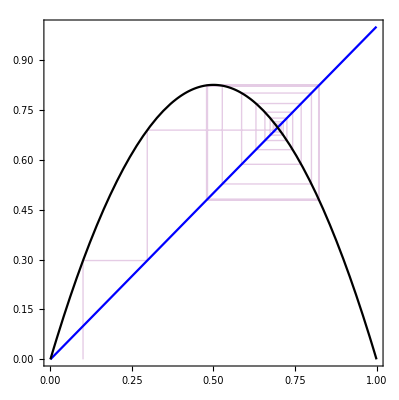

```mathematica
cobwebPlot[h[3.3], 0.1, 1000,{0,1}]
```

## Bifurcation Diagrams

Now that we can see what the sequences can be for a specific r value we want to also visualize what the general trajectory of these sequences could be as r gradually increases from 0 to 4. For a given r value, we will compute 500 iterates of h. Often, the iterates settle into a cycle, but there may be some initial noise before the cycle emerges. To ignore the noise, we will drop the first 100 iterates, as in the following function eventual[r]:

```mathematica
eventual[r_]:=Drop[ NestList[h[r],0.1,500],100]
```

Next let us define a set of points (r, y) just like we did in class for all values of y in eventual[r]:

```mathematica
points[r_]:={r,#}& /@eventual[r]
```

```mathematica
points[3.2];
```

Now that we have that done, let us make a plot of the points obtained for lots of values of r.  First let’s see the value of r to go from 0 to 4 and let us name it bifurcationPlot and later we will try to zoom in and see more of the “chaotic” part of the equation.

```mathematica
bifurcationPlot2=Graphics[ {PointSize[0.002],Opacity[0.1], Point[Flatten[Table[points[r],{r,3.4,4,.0005}],1]]}, AspectRatio->1/2,Frame->True]
```

-Graphics-

Now that we have initialized and visualized the logistic map let us pose some questions that helps us study more about these diagrams and try to find some conjunctures.

1.	 Is there some R value that will produce a cycle of length 3 or 4, where does it end? When does it stop being a sequence. 
3. 	Is this image created from the bifurcation plot a fractal, how do we know? Can we calculate the distance between the multiple bifurcation points. 
4. 	When zooming into r values between 3 and 4 we can see curves that look like they can fit a function, Can we find a similarity. 
5. 	What examples can you think of in extreme dependance of limits in a chaotic system.

## Number of sequences for different r values in h(x) and examples of extreme dependance of limits in a chaotic system.

To answer the first question let us look the graph we previously produced called bifurcation plot 2, this graph essentially puts every point after every Iteration, therefore we can see that at exactly 3.84  for a value of r there will most likely be 3 numbers that will be in sequence when trying to iteratively solve the equation. One important thing to look at is how there is an extreme dependance on limits in a chaotic system.  So to prove that this statement is correct let us look at 2 r values that are very close to each other and analyze their generation of a sequence. When looking at the graphs below we can see that the sequence of numbers is denoted by the darker purple lines that cross the inverted parabola which is the graph for the equation h(x) and the blue line x=y. Why does the value 3.84 have  3 numbers repeating in a sequence  but 3.86 doesn’t?  At what point is  this extreme dependance on limits relevant, in terms of  the r values?

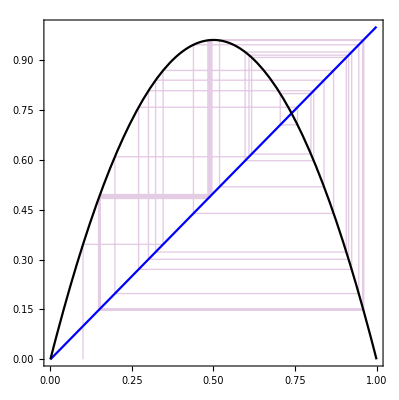

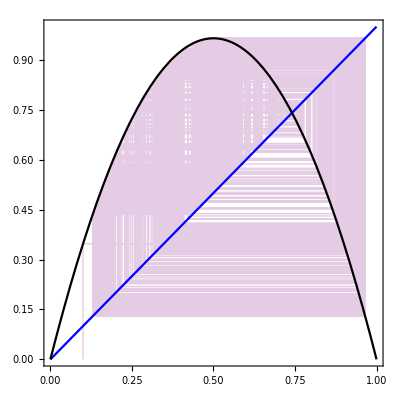

```mathematica
cobwebPlot[h[3.84], 0.1, 1000,{0,1}]
cobwebPlot[h[3.86], 0.1, 1000,{0,1}]
```

Just like the the sequence of 3 values we can also produce a sequence of 4 values, 5 values etc.. Let’s take a look at two r values that produce 4 and 5 sequences below just to try to prove that they exist.

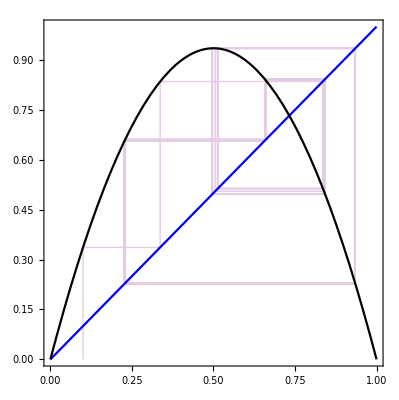

```mathematica
fourSeq = cobwebPlot[h[3.74], 0.1, 1000,{0,1}]
```

Therefore the more we zoom into the bifurcation plot the more we can find r values that have sequences of of 2, 3, 5, 6, etc.. When looking at the bifurcation plot we can see that values of r from 1 to approx 3 have a discernable sequence of either just 1 number or 2. What I am interested in asking is at what value of r does this become less of sequence and just a random chaotic group of numbers.

## Is the logistic map a fractal and how does that compare to the Mandelbrot set?

Before looking at comparisons  between the logistic map and the Mandelbrot set let’s look at what exactly the Mandelbrot set really is. The Mandelbrot set is a very famous fractal. It is defined to be the set of complex numbers c such that the function m_c(z)=z^2+c remains bounded in absolute value when iterated from z=0. Let’s write this out in a mathematica code chunk and try to plot it. We first want to iterate the fcuntion on complex numbers until the value exceeds some bound. Let us call this module numSteps and what this specifically calculates is the numberof setps until the bound is exceeded.

```mathematica
numSteps[f_,start_,bound_,maxSteps_:100]:=Module[{steps,z=start},
steps=0;
While[ Abs[z]≤ bound && steps<maxSteps,
z = f[z];
steps++
];
steps
]
```

```mathematica
m[c_][z_]:=z^2+c
```

Let's plot the Mandelbrot set:

```mathematica
DensityPlot[numSteps[m[x+y*I],0,50],{x,-2,1},{y,-1,1},PlotPoints->{500,100} , ColorFunction->"GreenPinkTones",AspectRatio->Automatic,PlotLegends->Automatic]
```

-Graphics-

Now to answer the question we posed is the Mandelbrot set connected to the logistic map in any way. One way that we can see is finding the ratios between the points at which the sequences divide into two. For example looking at our bifurcation plot manually finding the ration between approx 1 and 3 and so on. So let’s look at ways to do that. First we are going to call our bifurcation plot from earlier.

Let’s manually calculate the range between the points of bifurcation in the logistic map first. So we can see that the first one is distance between 1 - 3 and call it r1, next let’s look at r2 which will be  3 - 3.3. r3 will be between 3.43 - 3.52. 
r1 = 2
r2 = 0.43
r3 = 0.09
Therefore we can see that the range decreases as we increase the value of r.

Let' s manually calculate the range between the points of bifurcation in the Mandelbrot set. It seems like we should count the range towards the -ve x axis . So we can see that the first one is distance between 0.4 - (-ve 0.75) and call it r1, next let' s look at r2 which will be  -ve 0.45 - -ve 1.2.  r3 will be between -ve 1.25 - -ve 1.4. 
r1 = 1.15
r2 = 0.45
r3 = 0.15
Now that we can compare the values of r for both the maps we can see that the values of both r2’s are extremely close but the other r’s are a little off but it just shows that the Mandelbrot set or at least the ranges of the set are very similar to the ranges of the logistic map bifurcation graphs. We can somewhat conjuncture that the logitsic map is a fractal because we already know that the Mandelbrot set already is.

## Conclusion

In this project we were able to see what the logistic map is, the formula for it as well as the general trajectory of sequences it produces as r values within the formula gradually increases from 0 to 4. For a given r value, we we were able to compute 500 iterates of h and although the iterates settle into a cycle, but there may be some initial noise before the cycle emerges. After doing that er were able to answer some question after looking at the bifurcation plots for the logistic map. First we looked at different number of sequences for different r values in h(x) and examples of extreme dependance of limits in a chaotic system like this one. We were able to conclude that for values of r less that approx 3.6 there was somewhat of a sequence that appeared frequently but that stopped as the r value increased. We also saw an example of extreme dependance on limits when we saw differences in sequences for r values 3.84 and 3.86. Next we looked at whether or not the logistic map is a fractal and how it compares to the Mandelbrot set? We concluded that the logistic map is a fractal because we already know that the Mandelbrot set already is and the ranges in values between the specific points of bifurcation which we called r1, r2, and r3 show similarities.

## Limitations

One very important limitation that I had was that I couldn’t answer some of the question I posed in the beginning of the project. One example of these questions can be When zooming into r values between 3 and 4 we can see curves that look like they can fit a function, Can we find a similarity? How exactly can we tell that they fit a function. Another limitation that should be mentioned is when looking at the calculations of ranges for the Mandelbrot set as well as the bifurcation diagram is there an algorithm that specifically find the points when these bifurcations divide? rather than doing it manually. I should have also provided more examples to show that there is an extreme dependance of limits in a chaotic system.